Multi-Control Unitary Gates

Gray-Code Methodpaclet:QuantumMob/Q3/tutorial/MultiControlUnitaryGates#35322904 | Quadratic Implementationspaclet:QuantumMob/Q3/tutorial/MultiControlUnitaryGates#1081937375

A multi-control unitary gate is a natural generalization of a controlled-unitary gate, where the single control and target qubit are replaced by respective registers of multiple qubits. With m and n qubits in the control and target registers, respectively, and a unitary operator U on the target register, the m-control n-target U gate is defined by the mapping
	c⊗t↦c⊗(U^(c_1 c_2(⋯c)_m)t) ,
where c≡(c_1 c_2⋯ c_m)_2 and t≡(t_1 t_2⋯ t_n)_2. The unitary operator U on the target register takes effects only when every qubit in the control register is set to state |1⟩. In the quantum circuit model, a multi-control unitary gate is represented as

,

where m=3 and n=2 have been assumed form the particular concrete example.

Later we will see that the single-target case is sufficient to implement any unitary gate on multiple qubits, so here we will focus on it. In this case, the matrix representation takes the form in Figure 1 below.

(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | ⋱ | ⋮ | ⋮
0 | 0 | ⋯ | U_11 | U_12
0 | 0 | ⋯ | U_21 | U_22) .

Figure 1. The matrix representation of a multi-control unitary gate with a single target qubit.

In fact, the matrix in Figure 1 is a prototype form of a two-level unitary matrix on multiple qubits. Indeed, any two-level unitary matrix can be put into this form by exchanging columns and rows, which is equivalent to basis changes. Note also that an arbitrary two-qubit unitary gate can be decomposed into two-level unitary transformations. (see also tutorial document “Two-Qubit Gates”). These observations suggest that multi-control unitary gates comprise the vital part of decomposing arbitrary unitary gates on multiple qubits into elementary gates (see also tutorial document “Universal Quantum Computation”).

Moreover, reliable implementation of multi-control unitary gates is essential for many quantum algorithms. Notable examples are quantum decision problems and quantum search problems.

See also Section 2.3 of the Quantum Workbook (2022)https://doi.org/10.1007/978-3-030-91214-7.

ControlledGatepaclet:QuantumMob/Q3/ref/ControlledGateQuantumMob Package Symbol | Represents a multi-control multi-target unitary gate
GivensFactorpaclet:QuantumMob/Q3/ref/GivensFactorQuantumMob Package Symbol | Decomposes an arbitrary unitary gate into two-level unitary transformations
GivensRotationpaclet:QuantumMob/Q3/ref/GivensRotationQuantumMob Package Symbol | Represents a two-level unitary matrix
Toffolipaclet:QuantumMob/Q3/ref/ToffoliQuantumMob Package Symbol | The Toffoli gate
Fredkinpaclet:QuantumMob/Q3/ref/FredkinQuantumMob Package Symbol | The Fredkin gate
Deutschpaclet:QuantumMob/Q3/ref/DeutschQuantumMob Package Symbol | The Deutsch gate

Q3 functions related to multi-control unitary gates.

Make sure that the Q3: Symbolic Quantum Simulation package is loaded to use the demonstrations in this documentation.

```mathematica
Needs["QuantumMob`Q3`"]
```

Throughout this document, symbol S will be used to denote qubits and Pauli operators on them.

```mathematica
Let[Qubit,S]
```

Gray-Code Method

We first discuss one systematic method based on the Gray code to decompose a multi- control unitary gate into factors of either controlled-unitary or CNOT gates.

For example, consider a 3-control unitary gate as shown in the quantum circuit in Figure 2 below, where V is another unitary operator such that V^4=U. When every control qubit is set to |1⟩, all V gates in the diagram operate on the target qubit while the V^† gates are ineffective. To examine the case with the control qubits in a general state x_1⊗x_2⊗⋯⊗x_n, note that the gates on the target qubit are effective under the conditions specified in terms of the bit values at the bottom of the above diagram (see also the conditional-unitary gates). The conditions are systematically fulfilled by following the Gray code sequence, an arrange of bits such that two successive values differ in only one bit, the bit strings of which are indicated at the top of the diagram. The identity for the bitwise AND,

2^(n-1)(x_1 x_2(⋯x)_n)=∑_k_1 x_k_1-∑_(k_1<k_2) (x_k_1⊕x_k_2)+∑_(k_1<k_2<k_3) (x_k_1⊕x_k_2⊕x_k_3)-⋯+(-1)^(n-1)(x_1⊕x_2⊕⋯⊕x_n) ,

ensures that the above quantum circuit on the right-hand side reproduces the desired multi-control unitary gate on the left-hand side.

=-Graphics-

Figure 2. An implementation of a three-control unitary gate based on the Gray-code method (Barenco et al., 1995).

In general, an n-control unitary gate can be implemented by combining 2^(n-1) controlled-V gates, (2^(n-1)-1) controlled-V^† gates, and (2^n-2) CNOT gates, where V is a unitary operator satisfying V^(2^(n-1))=U. For a relatively small n (n≤8), the Gray-code method is known to be the most efficient method. However, it grows exponentially and eventually becomes impractical. Fortunately, there are alternative methods to overcome this exponential cost as discussed in the next section.

### Example

Let us consider a 3-control unitary gate.

```mathematica
Needs["QuantumMob`Q3`"]
```

```mathematica
Let[Qubit,S]
```

```mathematica
$L=3;
jj=Range[$L];
cc=S[jj,None];
```

This is the gate to operate on the target qubit.

```mathematica
T=S[$L+1,None];
op=Rotation[Pi/3,T[1]]//Elaborate
```

(√3)/2-1/2 ⅈ S_(,,4)^(,,X)

This decomposes the multi-control unitary gate based on the Gray code -- showing only a part of it. Each component is either CNOT or a two-qubit-control unitary gate.

```mathematica
gc=GrayControlledGate[cc,op]; gc[[;;3]]
```

{ControlledGate[{S_(,,1)→1},(2^(1/4) ⅇ^(-(ⅈ π)/24)+2^(1/4) ⅇ^((ⅈ π)/24))/(2 2^(1/4))+((2^(1/4) ⅇ^(-(ⅈ π)/24)-2^(1/4) ⅇ^((ⅈ π)/24)) S_(,,4)^(,,+))/(2 2^(1/4))+((2^(1/4) ⅇ^(-(ⅈ π)/24)-2^(1/4) ⅇ^((ⅈ π)/24)) S_(,,4)^(,,-))/(2 2^(1/4)),Label→V],CNOT[{S_(,,1)→1},{S_(,,2)}],ControlledGate[{S_(,,2)→1},(2^(1/4) ⅇ^(-(ⅈ π)/24)+2^(1/4) ⅇ^((ⅈ π)/24))/(2 2^(1/4))+((-2^(1/4) ⅇ^(-(ⅈ π)/24)+2^(1/4) ⅇ^((ⅈ π)/24)) S_(,,4)^(,,+))/(2 2^(1/4))+((-2^(1/4) ⅇ^(-(ⅈ π)/24)+2^(1/4) ⅇ^((ⅈ π)/24)) S_(,,4)^(,,-))/(2 2^(1/4)),Label→V^†]}

This is a quantum circuit model of the decomposition.

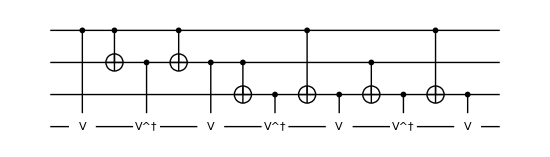

```mathematica
qc=QuantumCircuit@@gc
```

Finally check the result.

```mathematica
mat=Matrix[qc];
new=ControlledGate[cc,op]//Matrix;
mat-new//SimplifyThrough//ArrayZeroQ
```

True

Quadratic Implementations

Here we introduce two methods to implement multi-control unitary gates in terms of elementary gates the computational cost of which grows quadratically with the number of control qubits (Barenco et al., 1995).

The first method is based on the idea that has also been used for an implementation of the Toffoli gate and of the multi-control NOT gate with more control qubits. Given a unitary operator U on the target qubit, the implementation of the n-control U gate using this method is summarized in Figure 3. Let V be a unitary operator such that U=V^2. The center piece between the vertical dashed lines in the quantum circuit on the right-hand side represents a conditional unitary operator that operates V^† on the target qubit only when either (but not both) each of the first n−1 control qubits or the last control qubit is set to |1⟩. Combining this piece with a single-control V gate and a (n−2)-control V gate, one can rebuild the desired n-control U gate.

This method requires two multi-control NOT gates, each of which entails 𝒪(n) elementary gates. It is still to recursively implement (n−2)-control V gate. The recursion relation of the computational cost reveals that the overall cost of the implementation is quadratic in n, that is, 𝒪(n^2).

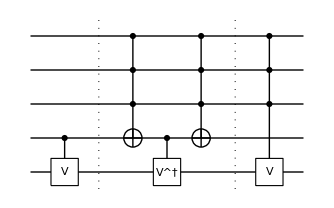
=-Graphics-

Figure 3. An implementation of a 4-control unitary gate, where V is the unitary operator satisfying U= V^2.

The second method, illustrated in Figure 4, is a generalization of the idea for the implementation of a controlled-unitary gate. Recall that one can always find three special unitary operators A, B, C and a global phase ϕ such that

U=ⅇ^(ⅈ ϕ)A X B X C ,

A B C=I .

A brief inspection asserts that the quantum circuit on the right-hand side of Figure 4 reproduces the n-control U gate on the left-hand side.

In this method, each of the two (n−1)-control NOT gates costs 𝒪(n) elementary gates. However, one still needs to recursively implement the (n − 1)-control phase gate with phase angle ϕ. Therefore, the computational cost of this method is of 𝒪(n^2) as well. One noteworthy fact is that the global phase ϕ of U vanishes if U is a special unitary operator (det U=1). This implies that a multi-control unitary gate for a special unitary operator requires only 𝒪(n) elementary gates; that is, the computational cost is linear.

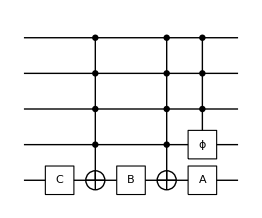
=-Graphics-

Figure 4. An implementation of a 4-control unitary gate, where the special unitary operators A, B, and C satisfy U=ⅇ^(ⅈ ϕ)A X B X C and A B C=I. The circuit element with label ‘ϕ’ denotes the relative phase gate by ϕ. If U itself is a special unitary operator (det U=1), then ϕ=0, and the cost is linear, 𝒪(n), in the number n of the qubits.

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪Quantum Computation: Overview
▪Quantum Information Systems with Q3

| Related Links
▪A. Barenco, et al. (1995)https://doi.org/10.1103/physreva.52.3457, Physical Review A 52, 3457 (1995), "Elementary gates for quantum computation."
▪J. A. Smolin and D. P. DiVincenzo (1996)https://doi.org/10.1103/PhysRevA.53.2855, Physical Review A 53, 2855  (1996), "Five two-bit quantum gates are sufficient to implement the quantum Fredkin gate." 
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).